## Лабораторная работа 1 Дунаев Виктор Андреевич 3 курс, 6 группа

## Задание 1

```mathematica
f[t_]:=t/2
```

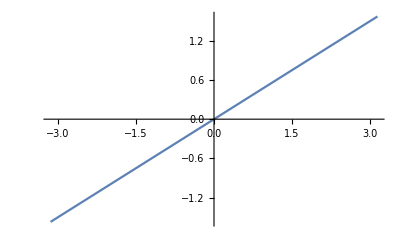

```mathematica
Plot[f[t],{t,-Pi,Pi}]
```

```mathematica
(* Коэффициенты Фурье по триг базису *)
```

```mathematica
CoefSin[N_,f_]:=(
list={};
For[i=1,i<=N,i++,
b=(1/Pi)*Integrate[f*Sin[i*t],{t,-Pi,Pi}];
AppendTo[list,b]
];
list
)
```

```mathematica
CoefSin[8,f[t]]
```

{1,-1/2,1/3,-1/4,1/5,-1/6,1/7,-1/8}

```mathematica
CoefCos[N_,f_]:=(
list = {};
For[i=1,i<=N,i++,
a=(1/Pi)*Integrate[f*Cos[i*t],{t,-Pi,Pi}];
AppendTo[list,a]
];
list
)
```

```mathematica
CoefCos[8,f[t]]
```

{0,0,0,0,0,0,0,0}

```mathematica
(* апроксимация и значение суммы ряда фурье *)
```

```mathematica
FourSer[N_, f_]:=(
listCos = CoefCos[N,f];
listSin = CoefSin[N,f];
sum = (1/(2*Pi))*Integrate[f,{t,-Pi,Pi}];
For[i=1,i<=N, i++,
sum+=listSin⟦i⟧*Sin[i*t];
sum+= listCos⟦i⟧*Cos[i*t];
];
sum
)
```

```mathematica
s = FourSer[8,f[t]]
```

Sin[t]-1/2 Sin[2 t]+1/3 Sin[3 t]-1/4 Sin[4 t]+1/5 Sin[5 t]-1/6 Sin[6 t]+1/7 Sin[7 t]-1/8 Sin[8 t]

```mathematica
(* спектральная диаграмма *)
```

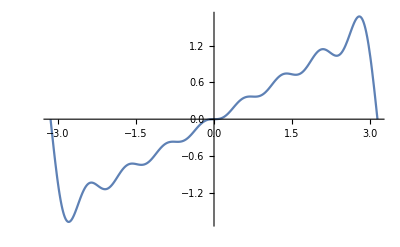

```mathematica
Plot[s,{t,-Pi,Pi}]
```

```mathematica
(* построить график ошибки N (t) = f(t) − S *)
```

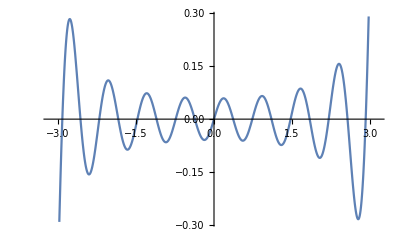

```mathematica
Plot[f[t]-s,{t,-Pi,Pi}]
```

## Задание 2

```mathematica
(* условие *)
```

```mathematica
f[t_]:=(
answer=0;
If[-Pi≤t≤0,
answer = 4-t;
];
If[0<t≤Pi,
answer = 7;
];
answer
)
```

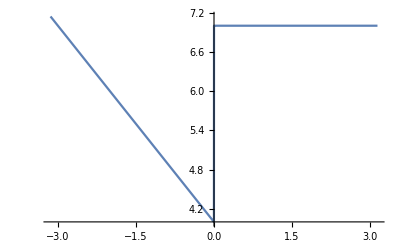

```mathematica
Plot[f[t],{t,-Pi,Pi}]
```

```mathematica
(* ищем сумму аналогично заданию 1 *)
```

```mathematica
CoefSin[N_]:=(
list={};
For[i=1,i<=N,i++,
b=(1/Pi)*Integrate[(4-t)*Sin[i*t],{t,-Pi,0}];
b+=(1/Pi)*Integrate[7Sin[i*t],{t,0,Pi}];
AppendTo[list,b];
b=0;
];
list
)
```

```mathematica
listSin = CoefSin[8]
```

{14/π+(-8-π)/π,1/2,14/(3 π)+(-8-π)/(3 π),1/4,14/(5 π)+(-8-π)/(5 π),1/6,2/π+(-8-π)/(7 π),1/8}

```mathematica
CoefCos[N_]:=(
list = {};
For[i=1,i<=N,i++,
a=(1/Pi)*Integrate[(4-t)*Cos[i*t],{t,-Pi,0}];
a+=(1/Pi)*Integrate[7Cos[i*t],{t,0,Pi}];
AppendTo[list,a];
a=0;
];
list
)
listCos = CoefCos[8]
```

{-2/π,0,-2/(9 π),0,-2/(25 π),0,-2/(49 π),0}

```mathematica
FourSer[N_]:=(
listCos = CoefCos[N];
listSin = CoefSin[N];
sum=Integrate[(4-t),{t,-Pi,0}];
sum+=Integrate[7,{t,0,Pi}];
sum*=1/(2Pi);
For[i=1,i<=N, i++,
sum+=listSin⟦i⟧*Sin[i*t];
sum+= listCos⟦i⟧*Cos[i*t];
];
sum
)
```

```mathematica
s=FourSer[8]
```

(11 π+π^2/2)/(2 π)-(2 Cos[t])/π-(2 Cos[3 t])/(9 π)-(2 Cos[5 t])/(25 π)-(2 Cos[7 t])/(49 π)+(14/π+(-8-π)/π) Sin[t]+1/2 Sin[2 t]+(14/(3 π)+(-8-π)/(3 π)) Sin[3 t]+1/4 Sin[4 t]+(14/(5 π)+(-8-π)/(5 π)) Sin[5 t]+1/6 Sin[6 t]+(2/π+(-8-π)/(7 π)) Sin[7 t]+1/8 Sin[8 t]

```mathematica
(* строим график *)
```

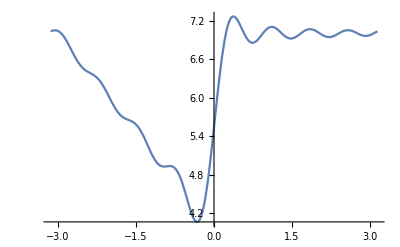

```mathematica
Plot[s,{t,-Pi,Pi}]
```

## Задание 3

```mathematica
(* условие *)
```

```mathematica
f[t_]:=4*t-3
```

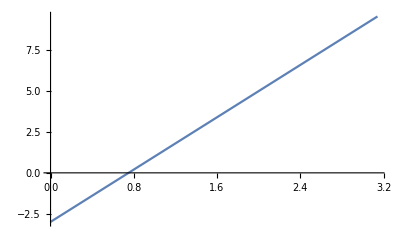

```mathematica
Plot[f[t],{t,0,Pi}]
```

```mathematica
(* а - синусами *)
```

```mathematica
CoefSin[N_,f_]:=(
list={};
For[i=1,i<=N,i++,
b=(1/Pi)*Integrate[f*Sin[i*t],{t,-Pi,Pi}];
AppendTo[list,b]
];
list
)
```

```mathematica
(* б - косинусами *)
```

```mathematica
CoefCos[N_,f_]:=(
list = {};
For[i=1,i<=N,i++,
a=(1/Pi)*Integrate[f*Cos[i*t],{t,-Pi,Pi}];
AppendTo[list,a]
];
list
)
```

```mathematica
FourSerOdd[N_, f_]:=(

listSin = CoefSin[N,f];
For[i=1,i<=N, i++,
sum+=listSin⟦i⟧*Sin[i*t];
];
sum
)
```

```mathematica
FourSerEven[N_, f_]:=(
listCos = CoefCos[N,f];
sum = (1/(2*Pi))*Integrate[f,{t,-Pi,Pi}];
For[i=1,i<=N, i++,
sum+= listCos⟦i⟧*Cos[i*t];
];
sum
)
```

```mathematica
fOdd = FourSerOdd[8,f[t]]
```

(11 π+π^2/2)/(2 π)-(2 Cos[t])/π-(2 Cos[3 t])/(9 π)-(2 Cos[5 t])/(25 π)-(2 Cos[7 t])/(49 π)+8 Sin[t]+(14/π+(-8-π)/π) Sin[t]-7/2 Sin[2 t]+8/3 Sin[3 t]+(14/(3 π)+(-8-π)/(3 π)) Sin[3 t]-7/4 Sin[4 t]+8/5 Sin[5 t]+(14/(5 π)+(-8-π)/(5 π)) Sin[5 t]-7/6 Sin[6 t]+8/7 Sin[7 t]+(2/π+(-8-π)/(7 π)) Sin[7 t]-7/8 Sin[8 t]

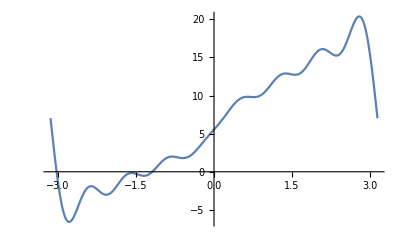

```mathematica
Plot[fOdd,{t,-Pi,Pi}]
```

```mathematica
fEven = FourSerEven[8,f[t]]
```

-3

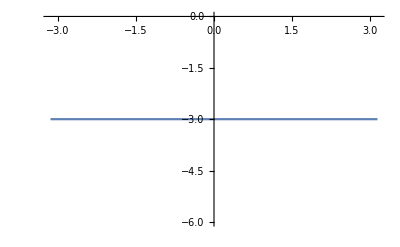

```mathematica
Plot[fEven,{t,-Pi,Pi}]
```

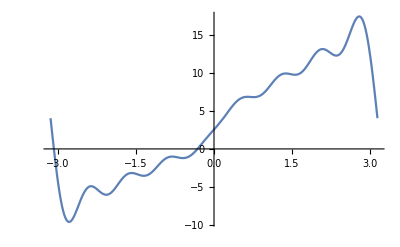

```mathematica
Plot[fEven+fOdd,{t,-Pi,Pi}]
```